## Initialization

```mathematica
Clear["Global`*"]
```

Approximate value of fN

```mathematica
fN1[a0in_]:=Module[{a0=a0in, R,N=121, fa0, G, Acell, L}, 
R = 0.2*a0;
fa0 = Sinh[R]Exp[R-a0]/a0;
G = 2π Exp[R] Sinh[R];
Acell = Sqrt[3]/2 a0^2;
L = Sqrt[ (N-7)Acell/π + (a0/2)^2];
fNest = 6fa0+G/Acell(Exp[-1.5 a0]- Exp[-L]);
fNinf = 6fa0+G/Acell Exp[-1.5 a0]
];
fN1[1]
```

0.940893

```mathematica
params = {Con -> 16,k-> 8,fN-> fNinf, n-> 2};
params2 = {Con -> 16,k-> 8, n-> 2};
```

Values for fN:
N=121, a0 = 0.5 => 
N=121, a0 = 1.5 =>

Updating function

```mathematica
S[x_]:=((Con-1)x+1);
f[xself_,xother_]:=(S[xself]+fN *S[xother])^n/(k^n+(S[xself]+fN *S[xother])^n);
```

Transforming Data

```mathematica
transformData[nsol_, xall_] :=Module[ {t,xvals}, 
xvals=Length/@(xself/.nsol);
t=Table[ ConstantArray[xall[[i]], xvals[[i]]], {i, 1, Length[xvals]}];
Flatten[Transpose/@Transpose[{t,xself/.nsol}], {1,2}]
];
```

## Mean-field approach

```mathematica
Plot3D[ {f[xself, xother] /. params, xself}, {xself,0,1}, {xother,0,1}, PlotRange-> All, BoxRatios->{1, 1, 1},ImageSize->Large, AxesLabel->{"x_self","x_other","f(x_self, x_other)"}, BaseStyle->{FontSize->20}, Mesh-> None, PlotStyle->Directive[Opacity[0.5]], Ticks-> {Automatic,Automatic, Automatic}]
```

-Graphics3D-

### Numerically find fixed points

```mathematica
dX = 0.001;
thisa0 =5;
sol = Table[
NSolve[ {((f[xself, xother ] - xself) /. params2 /. {fN-> fN1[thisa0]}) == 0,0≤xself≤ 1}, xself] ,
{xother,0,1, dX}];
plotdata = transformData[sol,Range[0,1,dX]];
```

Plot data

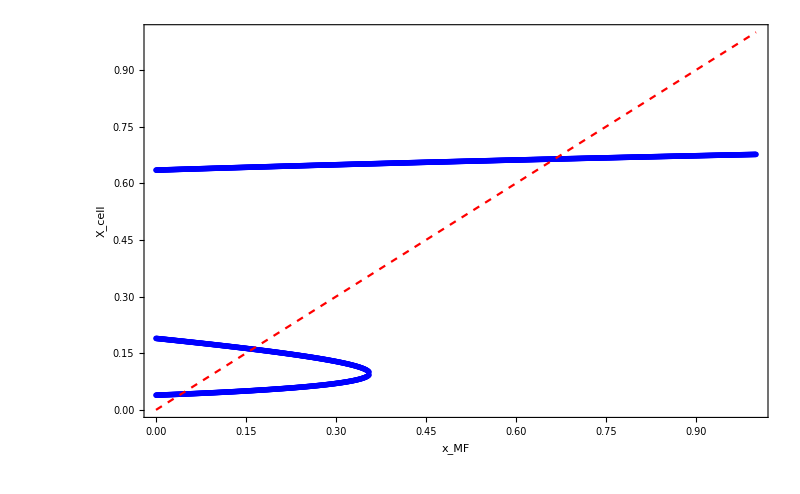

```mathematica
fstyle = Style[#,16] & ;
l1 = Placed[SwatchLegend[fstyle/@{"n=2"}, LegendMarkerSize->5],Above]; 
p1=ListPlot[plotdata, PlotStyle-> {Blue, PointSize-> 0.005}, AxesLabel-> {"x_other", "X_self"} ];
p2 = Plot[x, {x,0,1}, PlotStyle-> {Red, Dashed}];
fig2=Show[p1,p2,ImageSize-> 800,BaseStyle-> {FontSize-> 24}, Frame-> True, FrameLabel-> {"x_MF", "X_cell"}, PlotRange-> All, AxesOrigin-> {0,0}]
```

### Variability upper bound

Derive an upper bound for variability of ON and OFF cells.
E.g. take Δx_self=x_self(x_other=1)-x_self(x_other=0) for ON.

```mathematica
{xself/.Flatten[nsol[[-1]]]}[[1]]  - {xself/.Flatten[nsol[[1]]]}[[1]]
```

0.0817783

ON cells

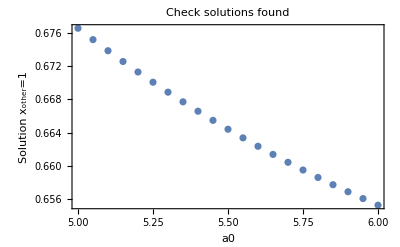

```mathematica
a0lims = {5.0,6.0,0.05}; (*start, end, di*)
a0data = Range[a0lims[[1]], a0lims[[2]], a0lims[[3]]];
solx0 = Table[
NSolve[ {((f[xself, 0] - xself) /. params2 /. {fN-> fN1[a0]}) == 0,0≤xself≤ 1}, xself] ,
{a0, a0lims[[1]],a0lims[[2]],a0lims[[3]]}];
solx1 = Table[
NSolve[ {((f[xself, 1] - xself) /. params2 /. {fN-> fN1[a0]}) == 0,0≤xself≤ 1}, xself] ,
{a0, a0lims[[1]],a0lims[[2]],a0lims[[3]]}];

plotDatax1 =transformData[solx1, a0data];
ListPlot[plotDatax1, PlotLabel->"Check solutions found", Frame->True, FrameLabel->{"a0", "Solution x_other=1"}]
```

OFF cells

```mathematica
x2Vals = ConstantArray[1,Length[a0data]]; (*Set to 1 very important, default if l==1 not found*)
xotherVals = Range[0,1,0.001];
Table[
a0=a0data[[a0ind]];
For[i=1, i< Length@xotherVals, i++,
l = Length@Flatten@NSolve[ {((f[xself, xotherVals[[i]]] - xself) /. params2 /. {fN-> fN1[a0]}) == 0,0≤xself≤ 1}, xself];
If[l==1,
x2Vals[[a0ind]]=xotherVals[[i-1]];
Print[x2Vals[[a0ind]]];
Break[];
];
],
{a0ind, 1, Length[a0data]}];
x2Vals
solx2 =Table[
NSolve[ {((f[ xself, x2Vals[[i]] ] - xself) /. params2 /. {fN-> fN1[a0data[[i]]]}) == 0,0≤xself≤ 1}, xself] ,
{i,1,Length[x2Vals]}];
```

0.355

0.372

0.388

0.406

0.424

0.442

0.462

0.482

0.503

0.524

0.547

0.57

0.594

0.619

0.644

0.671

0.699

0.728

0.757

0.788

0.82

{0.355,0.372,0.388,0.406,0.424,0.442,0.462,0.482,0.503,0.524,0.547,0.57,0.594,0.619,0.644,0.671,0.699,0.728,0.757,0.788,0.82}

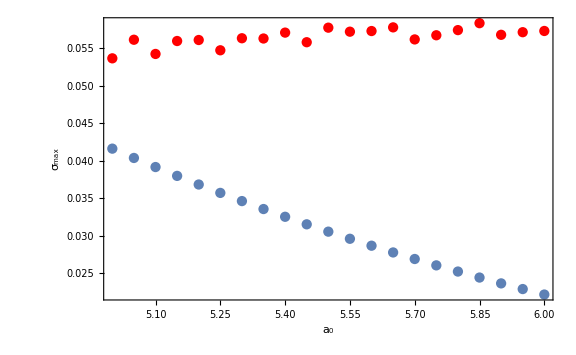

```mathematica
plotDataON = Transpose[{a0data,Max/@(xself/.solx1)-Max/@(xself/.solx0)}];
plotDataOFF = Transpose[{a0data,Min/@(xself/.solx2)-Min/@(xself/.solx0)}];
plot1=ListPlot[plotDataON]; (*, Frame->True, FrameLabel->{"a_0", "σ_max"},ImageSize-> Large,BaseStyle-> {FontSize-> 20}]*)
plot2=ListPlot[plotDataOFF, PlotStyle-> {Red}];
Show[plot1,plot2,Frame->True, FrameLabel->{"a_0", "σ_max"},ImageSize-> Large,BaseStyle-> {FontSize-> 20}, PlotRange-> All]
```

```mathematica
plotDataON
```

{{5.,0.0415901},{5.05,0.0403492},{5.1,0.0391396},{5.15,0.0379609},{5.2,0.0368126},{5.25,0.0356943},{5.3,0.0346053},{5.35,0.0335453},{5.4,0.0325136},{5.45,0.0315097},{5.5,0.0305332},{5.55,0.0295834},{5.6,0.02866},{5.65,0.0277623},{5.7,0.0268897},{5.75,0.0260419},{5.8,0.0252182},{5.85,0.0244181},{5.9,0.0236411},{5.95,0.0228867},{6.,0.0221544}}

```mathematica
(*
SetDirectory[NotebookDirectory[]];
Export["max_variance_cells_vs_a0_ON.XLS",plotDataON]
Export["max_variance_cells_vs_a0_OFF.XLS",plotDataOFF]
*)
```

plotDataON.XLS

plotDataOFF.XLS

## All fixed points vs a_0

### Numerically find fixed points

```mathematica
dX = 0.001;
thisa0 =5;
thisxsol = x/.NSolve[{f[x, x] - x == 0/. params2 /. {fN-> fN1[thisa0]}},x]
```

{0.664259,0.160797,0.0416104}

```mathematica
xsol=Table[x/.NSolve[{f[x, x] - x == 0/. params2 /. {fN-> fN1[a0]}},x∈ Reals], {a0,3.0,6.0,0.01}];
a0list = Range[3,6,0.01];
a0list2 = Table[ConstantArray[a0list[[i]],  xsol[[i]]//Length], {i,1, Length[xsol]}];
```

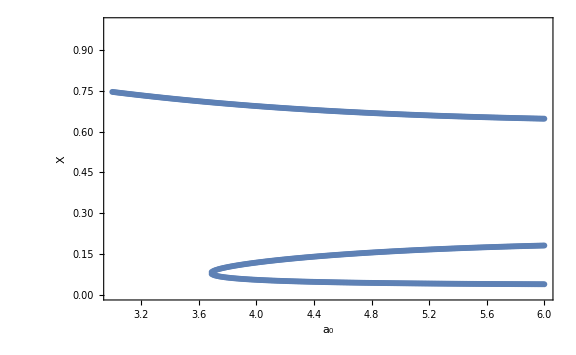

```mathematica
p1=ListPlot[Flatten[Transpose/@Transpose[{a0list2, xsol}], 1], ImageSize-> Large,BaseStyle-> {FontSize-> 20},Frame->True, FrameLabel-> {"a_0", "X"}, PlotRange-> {Automatic, {0,1}}]
```